```mathematica
FindInstance[x^3-11*y^3==1,{x,y},Integers](*First find an example of the Diophantine equation*)
```

{{x→1,y→0}}

```mathematica
Reduce[x^3-11*y^3==1,{x,y},Integers](*does the reduction over the Domain Z*)
```

```mathematica
x==1&&y==0
```

```mathematica
Reduce[Mod[x^2,1999]==1,{x,y},Integers]
```

y∈ℤ&&C[1]∈ℤ&&(x==1+1999 C[1]||x==1998+1999 C[1])

```mathematica
FindInstance[{3^x==y^2+2},{x,y},Integers]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[{3^x==2+y^2},{x,y},ℤ]

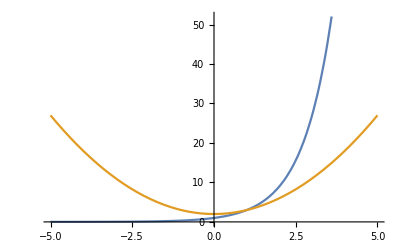

```mathematica
Plot[{y=3^x,y=x^2+2},{x,-5,5}]
```